Radiation pressure + Back-action evasion for nondegenerate internal squeezing

Attempt 1: Using Hamiltonian from Li et al, 2020

```mathematica
(* (*to-do: ability to turn RP on and off*)
β=(αGW Larm)/(2^(1/2)ℏ);
ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ);
*)
(*setting global assumptions*)
$Assumptions={Ω>0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0,Element[β,Reals],ρRP≥0,ρBAE≥0,Element[αOG,Reals]};

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mc=(γc-ⅈ Ω)Id-(ⅈ ρBAE)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMc=Inverse[Mc]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 Inverse[Ma]-χ^2({{0, 1}, {1, 0}}).Inverse[Mc].({{0, 1}, {1, 0}});
invMb=Inverse[Mb]//Simplify;

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ])//Simplify;
Rb=(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ])//Simplify;
Ra=(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ])//Simplify;
Rc=(-(1-Rpd)^(1/2)(2 γR)^(1/2)χ(2 γc)^(1/2)Γ.invMb.({{0, 1}, {1, 0}}).invMc.Inverse[Γ])//Simplify;
T=(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}}))//Simplify;
```

```mathematica
Sx=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc]),TimeConstraint->{1,10}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,10}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs=ComplexExpand[Abs[sigTransfer]]//Simplify;
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,10}];
```

(2 √(-(-1+Rpd) γR (γc^2+Ω^2)) ωs Abs[β])/(√(Ω^2 (γbtot γc+γa (γbtot+γc)-χ^2-Ω^2+ωs^2)^2+(γbtot Ω^2+γa (-γbtot γc+χ^2+Ω^2)+γc (Ω^2-ωs^2))^2))

```mathematica
(*signal transfer function -- demonstration of factor of two*)
FullSimplify[(T.({{1}, {1}}))/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG}];
FullSimplify[(T.ConjugateTranspose[T])/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG}];
Print["sig. transfer fn.: ",Simplify[ComplexExpand[Abs[%%[[2]][[1]] ]^2]]," vs ", %[[2,2]]]
```

sig. transfer fn.: (4 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2) vs (2 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2)

```mathematica
(* lossless reduction superceded by lossy reduction.
(*with R.P. and losses turned off, should match (also need to send β->-αOG)
NB: factor of two in denominator is from choice of signal transfer function (siding with Korobko convention over Li)*)
ComplexExpand[Simplify[Sh/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG}]]//FullSimplify
Simplify[Sx/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG}]//MatrixForm
Simplify[sigTransfer/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG}]//MatrixForm
*)
```

```mathematica
(*R.P. turned off, but lossy:
to-do: does it reduce to lossy sWLC?*)
FullSimplify[Sh/.{ρRP->0,ρBAE->0,β->-αOG}]
(*comparing to (ASDShsWLC)^2 from sWLC.nb*)
PSDShsWLC=1/((γc^2+Ω^2)4 αOG^2 ωs^2 γR)(
((γbtot-2γR)(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-(γbtot-2γR)(γa+γc)-γa γc+Ω^2)^2
+4γR γa ωs^2(γc^2+Ω^2)
+4γR γb(γa^2+Ω^2)(γc^2+Ω^2)
+4γR γc χ^2(γa^2+Ω^2)
+Rpd/(1-Rpd)((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2));
(PSDShsWLC/.{γb->γbtot-γR})//FullSimplify
Print["Rad. pressure off, reduces to lossy sWLC: ",%%%==%]
```

-1/(4 (-1+Rpd) αOG^2 γR (γc^2+Ω^2) ωs^2)((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

-1/(4 (-1+Rpd) αOG^2 γR (γc^2+Ω^2) ωs^2)((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

Rad. pressure off, reduces to lossy sWLC: True

```mathematica
(*simplfying full result, i.e. with R.P.*)
```

```mathematica
Sx22=Sx[[2,2]]
```

```mathematica
Sx22simple=ComplexExpand[Sx22]//Simplify
```

```mathematica
Collect[Sx22simple,{ρRP,ρBAE},Simplify]
```

-((8 (-1+Rpd) γR ρRP^2 (γc^2+Ω^2) ωs^2 (γa (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))+(γc χ^2+γbtot (γc^2+Ω^2)) ωs^2))/(Ω^4 (-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)^2))+(-2 γbtot γc χ^2 Ω^2+8 γc γR χ^2 Ω^2-8 Rpd γc γR χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)/(-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)-(8 (-1+Rpd) γR ρBAE^2 χ^2 (γa^2+Ω^2) (γbtot^2 γc Ω^2+γbtot χ^2 Ω^2+γa^2 (γbtot^2 γc+γbtot χ^2+γc Ω^2)+γa (2 γbtot γc+χ^2) ωs^2+γc (Ω^2-ωs^2)^2))/(Ω^4 (-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)^2)+(16 (-1+Rpd) γR ρBAE ρRP χ^2 ωs^2 (γa^2 γc (γbtot γc+χ^2+3 Ω^2)+γa (4 γbtot γc Ω^2+Ω^2 (χ^2+Ω^2)+γc^2 (-3 Ω^2+ωs^2))+Ω^2 (γbtot (-2 γc^2+Ω^2)+γc (-Ω^2+ωs^2))))/(Ω^4 (-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)^2)

```mathematica
(*recognise denominator as the same as sWLC*)
(((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2)==(-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4))//Simplify
```

True

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*signal is independent of R.P. and B.A.E. effects?*)
ComplexExpand[Abs[sigTransfer]^2]//Simplify
denom=Denominator[%]
(denom==((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2))//Simplify
```

-((4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)/(-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4))

-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4

True

```mathematica
(*checking other signal convention expansion --> appears to be dependent on ρRP, ρBAE
to-do: resolve this, since it implies different physics*)
(T.ConjugateTranspose[T])[[2,2]]//Simplify;
ComplexExpand[%]//Simplify
Collect[(2 γc^2 ρRP^2 χ^4+2 γc^4 ρRP^2 Ω^2+4 γc^2 ρBAE ρRP χ^2 Ω^2+4 γc^2 ρRP^2 χ^2 Ω^2+2 ρBAE^2 χ^4 Ω^2-4 ρBAE ρRP χ^4 Ω^2+2 ρRP^2 χ^4 Ω^2+4 γc^2 ρRP^2 Ω^4-4 ρBAE ρRP χ^2 Ω^4+4 ρRP^2 χ^2 Ω^4+2 ρRP^2 Ω^6+γc^2 χ^4 Ω^6+γc^4 Ω^8+2 γc^2 χ^2 Ω^8+χ^4 Ω^8+2 γc^2 Ω^10+2 χ^2 Ω^10+Ω^12+γbtot^2 (γc^2+Ω^2)^2 (2 ρRP^2+γa^2 Ω^4+Ω^6)+γa^2 (2 ρBAE^2 χ^4+γc^4 Ω^6+Ω^6 (χ^2+Ω^2)^2+γc^2 Ω^4 (χ^4+2 χ^2 Ω^2+2 Ω^4))-2 γc^4 Ω^6 ωs^2-2 γc^2 χ^2 Ω^6 ωs^2-4 γc^2 Ω^8 ωs^2-2 χ^2 Ω^8 ωs^2-2 Ω^10 ωs^2+γc^4 Ω^4 ωs^4+2 γc^2 Ω^6 ωs^4+Ω^8 ωs^4-2 γa γc χ^2 (2 ρBAE ρRP (χ^2+2 Ω^2)+Ω^4 (γc^2+Ω^2) ωs^2)-2 γbtot (γa^2 γc χ^2 Ω^4 (γc^2+Ω^2)+γc χ^2 (γc^2 (2 ρRP^2+Ω^6)+Ω^2 (-4 ρBAE ρRP+2 ρRP^2+Ω^6))-γa (-2 ρBAE ρRP χ^2 Ω^2+γc^4 Ω^4 ωs^2+Ω^8 ωs^2+2 γc^2 (ρBAE ρRP χ^2+Ω^6 ωs^2)))),{ρRP,ρBAE},Simplify]
(*to-do: fix this!*)
```

-((2 (-1+Rpd) β^2 γR ωs^2 (2 γc^2 ρRP^2 χ^4+2 γc^4 ρRP^2 Ω^2+4 γc^2 ρBAE ρRP χ^2 Ω^2+4 γc^2 ρRP^2 χ^2 Ω^2+2 ρBAE^2 χ^4 Ω^2-4 ρBAE ρRP χ^4 Ω^2+2 ρRP^2 χ^4 Ω^2+4 γc^2 ρRP^2 Ω^4-4 ρBAE ρRP χ^2 Ω^4+4 ρRP^2 χ^2 Ω^4+2 ρRP^2 Ω^6+γc^2 χ^4 Ω^6+γc^4 Ω^8+2 γc^2 χ^2 Ω^8+χ^4 Ω^8+2 γc^2 Ω^10+2 χ^2 Ω^10+Ω^12+γbtot^2 (γc^2+Ω^2)^2 (2 ρRP^2+γa^2 Ω^4+Ω^6)+γa^2 (2 ρBAE^2 χ^4+γc^4 Ω^6+Ω^6 (χ^2+Ω^2)^2+γc^2 Ω^4 (χ^4+2 χ^2 Ω^2+2 Ω^4))-2 γc^4 Ω^6 ωs^2-2 γc^2 χ^2 Ω^6 ωs^2-4 γc^2 Ω^8 ωs^2-2 χ^2 Ω^8 ωs^2-2 Ω^10 ωs^2+γc^4 Ω^4 ωs^4+2 γc^2 Ω^6 ωs^4+Ω^8 ωs^4-2 γa γc χ^2 (2 ρBAE ρRP (χ^2+2 Ω^2)+Ω^4 (γc^2+Ω^2) ωs^2)-2 γbtot (γa^2 γc χ^2 Ω^4 (γc^2+Ω^2)+γc χ^2 (γc^2 (2 ρRP^2+Ω^6)+Ω^2 (-4 ρBAE ρRP+2 ρRP^2+Ω^6))-γa (-2 ρBAE ρRP χ^2 Ω^2+γc^4 Ω^4 ωs^2+Ω^8 ωs^2+2 γc^2 (ρBAE ρRP χ^2+Ω^6 ωs^2)))))/(Ω^4 (-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)^2))

2 ρBAE^2 χ^4 (γa^2+Ω^2)+2 ρRP^2 (γc^2+Ω^2) (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-4 ρBAE ρRP χ^2 (γa γbtot (-γc^2+Ω^2)+Ω^2 (-2 γbtot γc-γc^2+χ^2+Ω^2)+γa γc (χ^2+2 Ω^2))+Ω^4 (γc^2+Ω^2) (-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+γbtot^2 Ω^2 (γc^2+Ω^2)+γa^2 (-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+2 γa (-γc χ^2+γbtot (γc^2+Ω^2)) ωs^2+γc^2 ωs^4+Ω^2 ωs^4)

```mathematica
(*plot params -- from sWLC model*)
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
Larm=4 10^3(*m*);
Pcirc=3 10^6(*J/s*);
λ0=2 10^-6(*m*);
ω0=2π c/λ0;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];
γR=2π 500 (*Hz*);
ωs=10γR;
β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match
β=(αGW Larm)/(2^(1/2)ℏ);
ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm|*)
M=200(*kg*);
μ=M/4;
ρ=(2^(1/2)ℏ β^2)/(Larm^2 μ);
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γcFn[Tlc_,symSRM_]:=If[symSRM,γR+-1/(2 τRoundTripSRC)Log[1-Tlc],-1/(2 τRoundTripSRC)Log[1-Tlc]]
(*plotting sensitivity -- un-simplified Sh*)
QNwRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Sqrt[Sx[[2,2]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
sigwRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=sigTransferAbs/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
ASDShwRP[Ω0_,χ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Sqrt[Sh]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
```

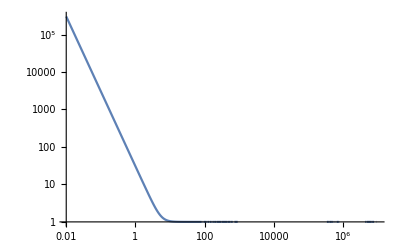

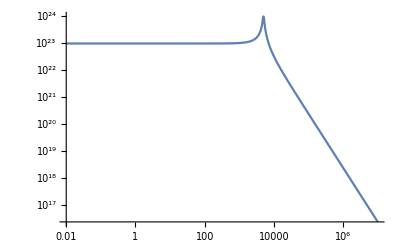

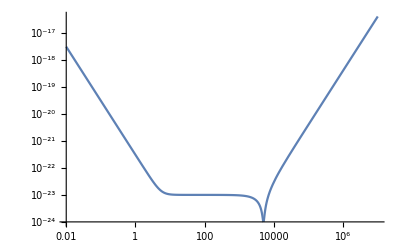

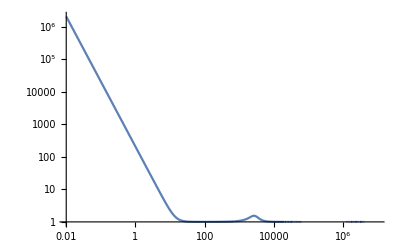

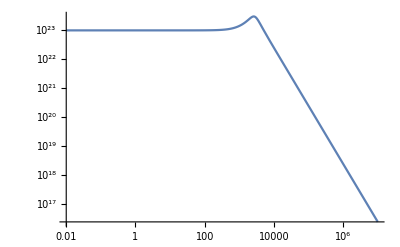

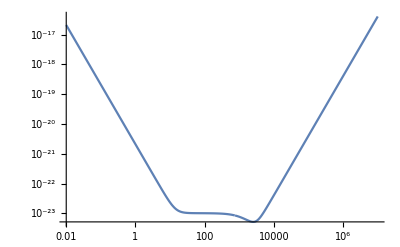

```mathematica
(*to-do: copy plotting functions from sWLC*)

LogLogPlot[QNwRP[2π f,0,0,0,0,0],{f,10^-2,10^7}]
LogLogPlot[sigwRP[2π f,0,0,0,0,0],{f,10^-2,10^7}]
LogLogPlot[ASDShwRP[2π f,0,0,0,0,0],{f,10^-2,10^7}]

LogLogPlot[QNwRP[2π f,1ωs,0,0,0.1,0],{f,10^-2,10^7}]
LogLogPlot[sigwRP[2π f,1ωs,0,0,0.1,0],{f,10^-2,10^7}]
LogLogPlot[ASDShwRP[2π f,1ωs,0,0,0.1,0],{f,10^-2,10^7}]

valsList={
{0,0,0,0,0},
{1ωs,0.1,0.1,0.1,0.1}}
```